```mathematica
CalculateInOutFormulaKeep[g_]:=CalculateInOutFormulaKeep[g,VertexList[g]]
```

```mathematica
LetterAssoc[n_]:=Table[k->Symbol[MyLetter[k]],{k,n}]
```

```mathematica
LetterAssoc[10]
```

{1→a,2→b,3→c,4→d,5→e,6→f,7→g,8→h,9→i,10→j}

```mathematica
MakeSym[s1_,s2_]:=Block[{n1=If[StringQ[s1],s1, SymbolName[s1]],n2=If[StringQ[s2],s2,SymbolName[s2]]},
Symbol[StringJoin[Sort[Join[Characters[n1],Characters[n2]]]]]
]
```

```mathematica
MakeSym[ac,bd]
```

abcd

```mathematica
CalculateInOutFormulaKeep[g_,sets_]:=CalculateInOutFormulaKeep[g,sets,LetterAssoc[Length[sets]]]
```

```mathematica
FindFullFormulaWithPrefix[g_,prefix_]:=Fold [Plus,Map[ChangeSymbol[#,prefix]&,FindFullFormula[g]]]
```

```mathematica
FindFullFormulaWithPrefix2 [g_,pref_]:=Block[{res},
(*Print[FindFullFormula[g]];*)
res=Fold [Plus,Table[pref,FindFullFormula[g]]];
(*Print[{"FindFullFormulaWithPrefix2",Graph[g,VertexLabels->"Name"],pref,res}];*)
res
];
```

```mathematica
CalculateInOutFormulaKeep[g_,sets_, repl2_]:=Block[{
currentEdge, 
edges, 
pos,
isInOut, gContract, gRemove, gIn, gOut, result, resIn, resOut, resContract, resRemove, repVertex, in, out,inVertex,outVertex,
node,
  maxRep, minRep, newRep=Association[repl2],s1,s2},
(*Print[{Graph[g,VertexLabels->"Name"],sets,repl2}];*)
If[VertexCount[g]==0,
Print["VertexCount is zero",g,sets];
Return[1]
];
(* if there is no set, we have a problem *)
If[Length[sets]==0,
Print["No more sets"];
Interrupt[];
];
(* if there is only one set, we are done *)
If[Length[sets]==1,
node=First[sets];
result=Lookup[newRep,node];
Return[result];
];

(* there is more than 1 set : we define in to be the first set, out to be thejoin of the rest *)
in=First[sets];
out=Rest[sets];

(* the whole goal is to remove the  in *)
(* as long as there is an edge between in and out we remove and contract it and recurse *)
edges=EdgeList[g,in<->_];
If[edges≠{},
currentEdge=First[edges];
If[currentEdge[[1]]≠in, 
(* make sure the first vertex is in "in" an dthe second in "out" *)
currentEdge=UndirectedEdge[currentEdge[[2]],currentEdge[[1]]]
];
(* the remove is easy, it uses the same vertex set and the same replacement *)
gRemove=EdgeDelete[g,currentEdge];
resRemove=CalculateInOutFormulaKeep[gRemove,sets,repl2];

(* no wthe contract *)
inVertex = currentEdge[[1]];
outVertex = currentEdge[[2]];
s1=Lookup[newRep,inVertex];
s2=Lookup[newRep,outVertex];

minRep=MakeSym[s1,s2];
newRep[inVertex]=minRep;
newRep[outVertex]=minRep;
gContract=GContract[g,currentEdge];
repVertex={inVertex->outVertex}; (* replace the in by the out since we want ot get rid of the in *)
gContract=Graph[VertexList[gContract]/.repVertex,Map[#[[1]]<->#[[2]]/.repVertex&,EdgeList[gContract]]];
resContract=CalculateInOutFormulaKeep[gContract,sets,newRep];
result=resRemove-resContract;
Return[result]
];

(* there are no more edges between in and out so we compute in and recurse with the rest *)
gIn=Subgraph[g,in];
gOut=Subgraph[g,out];
resIn=If[VertexCount[gIn]==0,1,Lookup[newRep,First[VertexList[gIn]]]];
resOut=If[VertexCount[gOut]==0,1,CalculateInOutFormulaKeep[gOut,Rest[sets],repl2]];
Return[resIn*resOut]
]
```

```mathematica
CalculateInOutFormulaKeep[CycleGraph[3]]//Factor
```

2 abc-ac b-a bc-ab c+a b c

```mathematica
ChromaticPolynomial[CycleGraph[3],x]
```

2 x-3 x^2+x^3

```mathematica
2 abc-ac b-ab c+a (-bc+b c)//Expand
```

2 abc-ac b-a bc-ab c+a b c

```mathematica
CalculateInOutFormulaKeep[CycleGraph[4]]//Factor
```

-3 abcd+acd b+ad bc+a bcd+abd c-ad b c+ab cd-a b cd+abc d-a bc d-ab c d+a b c d

```mathematica
CalculateInOutFormulaKeep[CycleGraph[5]]//Factor
```

4 abcde-acde b-ade bc-ae bcd-a bcde-abde c+ade b c-abe cd+ae b cd-ab cde+a b cde-abce d+ae bc d+abe c d-ae b c d-abc de+a bc de+ab c de-a b c de-abcd e+a bcd e+ab cd e-a b cd e+abc d e-a bc d e-ab c d e+a b c d e

```mathematica
CalculateInOutFormulaKeep[CompleteGraph[5]]//Factor//Length
```

52

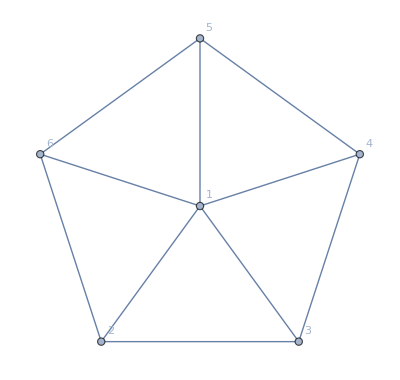

```mathematica
WheelGraph[6,VertexLabels->"Name"]
```

```mathematica
f1=CalculateInOutFormulaKeep[WheelGraph[6]]
```

SymbolName::sym: Argument Lookup[newRep,inVertex] at position 1 is expected to be a symbol.

SymbolName::sym: Argument Lookup[newRep,outVertex] at position 1 is expected to be a symbol.

Characters::argx: Characters called with 2 arguments; 1 argument is expected.

StringJoin::string: String expected at position 1 in StringJoin[Characters[SymbolName[Lookup[newRep,inVertex]],SymbolName[Lookup[newRep,outVertex]]]].

Symbol::string: String expected at position 1 in Symbol[StringJoin[Characters[SymbolName[Lookup[newRep,inVertex]],SymbolName[Lookup[newRep,outVertex]]]]].

SymbolName::sym: Argument Lookup[newRep,inVertex] at position 1 is expected to be a symbol.

General::stop: Further output of SymbolName::sym will be suppressed during this calculation.

Characters::argx: Characters called with 2 arguments; 1 argument is expected.

StringJoin::string: String expected at position 1 in StringJoin[Characters[SymbolName[Lookup[newRep,inVertex]],SymbolName[Lookup[newRep,outVertex]]]].

Symbol::string: String expected at position 1 in Symbol[StringJoin[Characters[SymbolName[Lookup[newRep,inVertex]],SymbolName[Lookup[newRep,outVertex]]]]].

Characters::argx: Characters called with 2 arguments; 1 argument is expected.

General::stop: Further output of Characters::argx will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[Characters[SymbolName[Lookup[newRep,inVertex]],SymbolName[Lookup[newRep,outVertex]]]].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::string: String expected at position 1 in Symbol[StringJoin[Characters[SymbolName[Lookup[newRep,inVertex]],SymbolName[Lookup[newRep,outVertex]]]]].

General::stop: Further output of Symbol::string will be suppressed during this calculation.

-30 Lookup[newRep,node]+30 Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]]-21 Lookup[newRep,First[VertexList[gIn]]] (-Lookup[newRep,node]+Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]])+3 Lookup[newRep,First[VertexList[gIn]]] (2 Lookup[newRep,node]-2 Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]]+Lookup[newRep,First[VertexList[gIn]]] (-Lookup[newRep,node]+Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]]))+9 Lookup[newRep,First[VertexList[gIn]]] (Lookup[newRep,node]-Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]]+Lookup[newRep,First[VertexList[gIn]]] (-Lookup[newRep,node]+Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]]))-Lookup[newRep,First[VertexList[gIn]]] (-2 Lookup[newRep,node]+2 Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]]-Lookup[newRep,First[VertexList[gIn]]] (-Lookup[newRep,node]+Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]])+Lookup[newRep,First[VertexList[gIn]]] (2 Lookup[newRep,node]-2 Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]]+Lookup[newRep,First[VertexList[gIn]]] (-Lookup[newRep,node]+Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]])))-Lookup[newRep,First[VertexList[gIn]]] (-4 Lookup[newRep,node]+4 Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]]-3 Lookup[newRep,First[VertexList[gIn]]] (-Lookup[newRep,node]+Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]])+Lookup[newRep,First[VertexList[gIn]]] (Lookup[newRep,node]-Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]]+Lookup[newRep,First[VertexList[gIn]]] (-Lookup[newRep,node]+Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]])))-3 Lookup[newRep,First[VertexList[gIn]]] (-Lookup[newRep,node]+Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]]-Lookup[newRep,First[VertexList[gIn]]] (-Lookup[newRep,node]+Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]])+Lookup[newRep,First[VertexList[gIn]]] (Lookup[newRep,node]-Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]]+Lookup[newRep,First[VertexList[gIn]]] (-Lookup[newRep,node]+Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]])))+Lookup[newRep,First[VertexList[gIn]]] (4 Lookup[newRep,node]-4 Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]]+3 Lookup[newRep,First[VertexList[gIn]]] (-Lookup[newRep,node]+Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]])-2 Lookup[newRep,First[VertexList[gIn]]] (Lookup[newRep,node]-Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]]+Lookup[newRep,First[VertexList[gIn]]] (-Lookup[newRep,node]+Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]]))+Lookup[newRep,First[VertexList[gIn]]] (-Lookup[newRep,node]+Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]]-Lookup[newRep,First[VertexList[gIn]]] (-Lookup[newRep,node]+Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]])+Lookup[newRep,First[VertexList[gIn]]] (Lookup[newRep,node]-Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]]+Lookup[newRep,First[VertexList[gIn]]] (-Lookup[newRep,node]+Lookup[newRep,node] Lookup[newRep,First[VertexList[gIn]]]))))

```mathematica
FindFullFormula[WheelGraph[6]]
```

{v1x2x3x4x5x6,v1x2x3x46x5,v1x2x36x4x5,v1x2x35x4x6,v1x2x35x46,v1x25x3x4x6,v1x25x3x46,v1x25x36x4,v1x24x3x5x6,v1x24x36x5,v1x24x35x6}